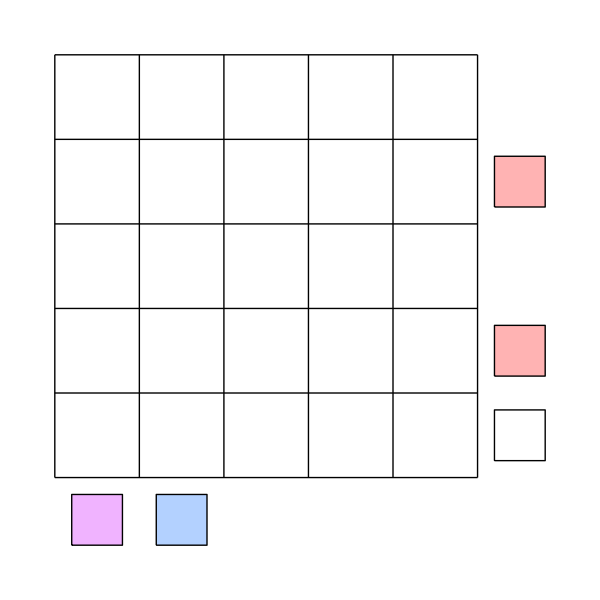
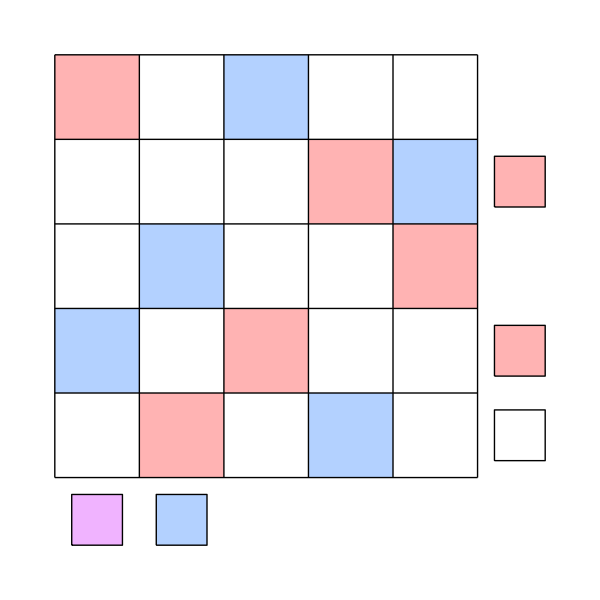

-Graphics-  -Graphics-

```mathematica
n=4;
```

```mathematica
p=Permutations[Range[n]];
```

```mathematica
s=Select[Flatten[Outer[List,p,p,1],1],Min[Abs[#[[1]]-#[[2]]]]>0&];
```

```mathematica
r[x_,y_]:={Hue[0,.3],Rectangle[{x-1,y-1},{x,y}]}
```

```mathematica
b[x_,y_]:={Hue[.6,.3],Rectangle[{x-1,y-1},{x,y}]}
```

```mathematica
pic[L_]:=Style[Graphics[{
MapIndexed[r[#1,#2[[1]]]&,L[[1]]],MapIndexed[b[#1,#2[[1]]]&,L[[2]]],Black,
Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}]
},ImageSize->20n],Antialiasing->False]
```

```mathematica
beforepic[L_,sides_]:=Style[Graphics[{
Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}],
Map[If[#>n,{colspec[L,#],Rectangle[{n+.2,#-.8-n},{n+.8,#-.2-n}],Black,Line[{{n+.2,#-.8-n},{n+.8,#-.8-n},{n+.8,#-.2-n},{n+.2,#-.2-n},{n+.2,#-.8-n}}]},{colspec[L,#],Rectangle[{#-.8,-.8},{#-.2,-.2}],Black,Line[{{#-.8,-.8},{#-.8,-.2},{#-.2,-.2},{#-.2,-.8},{#-.8,-.8}}]}]&,sides]
},ImageSize->20(n+.8)],Antialiasing->False]
```

```mathematica
pic[L_,sides_]:=Style[Graphics[{
MapIndexed[r[#1,#2[[1]]]&,L[[1]]],MapIndexed[b[#1,#2[[1]]]&,L[[2]]],Black,
Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}],
Map[If[#>n,{colspec[L,#],Rectangle[{n+.2,#-.8-n},{n+.8,#-.2-n}],Black,Line[{{n+.2,#-.8-n},{n+.8,#-.8-n},{n+.8,#-.2-n},{n+.2,#-.2-n},{n+.2,#-.8-n}}]},{colspec[L,#],Rectangle[{#-.8,-.8},{#-.2,-.2}],Black,Line[{{#-.8,-.8},{#-.8,-.2},{#-.2,-.2},{#-.2,-.8},{#-.8,-.8}}]}]&,sides]
},ImageSize->20(n+.8)],Antialiasing->False]
```

```mathematica
sight[{red_,blue_}]:=(d={Min[red,blue]-1,Abs[red-blue]-1,n-Max[red,blue]};
If[red>blue,Which[d[[3]]>Max[d[[1]],d[[2]]],1,d[[2]]>Max[d[[1]],d[[3]]],3,d[[1]]>Max[d[[2]],d[[3]]],2,True,4],Which[d[[3]]>Max[d[[1]],d[[2]]],2,d[[2]]>Max[d[[1]],d[[3]]],3,d[[1]]>Max[d[[2]],d[[3]]],1,True,4]])
```

```mathematica
rows[L_]:=Map[sight,Transpose[L],1]
```

```mathematica
c[L_]:=Table[Position[L,i][[1,1]],{i,1,n}]
```

```mathematica
columns[L_]:=Map[sight,Transpose[Map[c,L]],1]
```

```mathematica
col={Hue[0,.3],Hue[.6,.3],Hue[.8,.3],White};
```

```mathematica
colspec[L_,i_]:=col[[spectrum[L][[i]]]]
```

```mathematica
spectrum[L_]:=columns[L]~Join~rows[L]
```

```mathematica
For[i=1,i≤2,i++,
For[j=5,j≤6,j++,
For[k=j+1,k≤13-j,k++,
For[ci=1,ci≤4,ci++,
For[cj=1,cj≤4,cj++,
For[ck=1,ck≤4,ck++,
poss=Select[s,spectrum[#][[i]]==ci&&spectrum[#][[j]]==cj&&spectrum[#][[k]]==ck&];
If[Length[poss]==1,Print[beforepic[poss[[1]],{i,j,k}],"  ",pic[poss[[1]],{i,j,k}]]]]]]]]]
```

```mathematica
n=5;
```

```mathematica
p=Permutations[Range[n]];
```

```mathematica
s=Select[Flatten[Outer[List,p,p,1],1],Min[Abs[#[[1]]-#[[2]]]]>0&];
```

```mathematica
ran:=RandomInteger[{1,2n}];
```

```mathematica
ranc:=RandomInteger[{1,4}];
```

```mathematica
ranw:=RandomInteger[{1,3}];
```

```mathematica
For[ct=1,ct>0,ct++,
i=ran;j=ran;k=ran;l=ran;m=ran;
If[Length[Union[{i,j,k,l,m}]]==5,
ci=ranw;cj=ranw;ck=ranw;cl=ranw;cm=ranw;
poss=Select[s,spectrum[#][[i]]==ci&&spectrum[#][[j]]==cj&&spectrum[#][[k]]==ck&&spectrum[#][[l]]==cl&&spectrum[#][[m]]==cm&];
If[Length[poss]==1,Print[beforepic[poss[[1]],{i,j,k,l,m}],"  ",pic[poss[[1]],{i,j,k,l,m}]]]]]
```

```mathematica
For[ct=1,ct>0,ct++,
i=ran;j=ran;k=ran;l=ran;
If[Length[Union[{i,j,k,l}]]==4,
ci=4;cj=ranw;ck=ranw;cl=ranw;
poss=Select[s,spectrum[#][[i]]==ci&&spectrum[#][[j]]==cj&&spectrum[#][[k]]==ck&&spectrum[#][[l]]==cl&];
If[Length[poss]==1,Print[beforepic[poss[[1]],{i,j,k,l}],"  ",pic[poss[[1]],{i,j,k,l}]]]]]
```

```mathematica
n=6;
```

```mathematica
p=Permutations[Range[n]];
```

```mathematica
s=Select[Flatten[Outer[List,p,p,1],1],Min[Abs[#[[1]]-#[[2]]]]>0&];
```

```mathematica
Length[s]
```

190800

```mathematica
For[ct=1,ct>0,ct++,
i=ran;j=ran;k=ran;l=ran;m=ran;h=ran;g=ran;
If[Length[Union[{i,j,k,l,m,h,g}]]==7,
ci=ranc;cj=ranc;ck=ranc;cl=ranc;cm=ranc;ch=ranc;cg=ranc;
poss=Select[s,spectrum[#][[i]]==ci&&spectrum[#][[j]]==cj&&spectrum[#][[k]]==ck&&spectrum[#][[l]]==cl&&spectrum[#][[m]]==cm&&spectrum[#][[g]]==cg&&spectrum[#][[h]]==ch&];
If[Length[poss]==1,Print[beforepic[poss[[1]],{i,j,k,l,m,g,h}],"  ",pic[poss[[1]],{i,j,k,l,m,g,h}]]]]]
```

$Aborted

```mathematica
n=4;
```

```mathematica
p=Permutations[Range[n]];
```

```mathematica
s=Select[Flatten[Outer[List,p,p,1],1],Min[Abs[#[[1]]-#[[2]]]]>0&];
```

```mathematica
r[x_,y_]:={Text[Style["A",FontSize->16],{x-1/2,y-.55}]}
```

```mathematica
b[x_,y_]:={Text[Style["B",FontSize->16],{x-1/2,y-.55}]}
```

```mathematica
pic[L_]:=Style[Graphics[{
MapIndexed[r[#1,#2[[1]]]&,L[[1]]],MapIndexed[b[#1,#2[[1]]]&,L[[2]]],Black,
Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}]
},ImageSize->20n],Antialiasing->False]
```

```mathematica
beforepic[L_,sides_]:=Style[Graphics[{
Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}],
Map[If[#>n,Which[
spectrum[L][[#]]==1,Text[Style["A",FontSize->12],{n+.5,#-.5-n}],spectrum[L][[#]]==2,Text[Style["B",FontSize->12],{n+.5,#-.5-n}],spectrum[L][[#]]==3,Text[Style["AB",FontSize->12],{n+.5,#-.5-n}],spectrum[L][[#]]==4,Text[Style["O",FontSize->12],{n+.5,#-.5-n}]],Which[
spectrum[L][[#]]==1,Text[Style["A",FontSize->12],{#-.5,-.5}],spectrum[L][[#]]==2,Text[Style["B",FontSize->12],{#-.5,-.5}],spectrum[L][[#]]==3,Text[Style["AB",FontSize->12],{#-.5,-.5}],spectrum[L][[#]]==4,Text[Style["O",FontSize->12],{#-.5,-.5}]]]&,sides]
},ImageSize->20(n+1),PlotRange->{{0,n+1},{-1,n}}],Antialiasing->False]
```

```mathematica
pic[L_,sides_]:=Style[Graphics[{
MapIndexed[r[#1,#2[[1]]]&,L[[1]]],MapIndexed[b[#1,#2[[1]]]&,L[[2]]],Black,
Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}],
Map[If[#>n,Which[
spectrum[L][[#]]==1,Text[Style["A",FontSize->12],{n+.5,#-.5-n}],spectrum[L][[#]]==2,Text[Style["B",FontSize->12],{n+.5,#-.5-n}],spectrum[L][[#]]==3,Text[Style["AB",FontSize->12],{n+.5,#-.5-n}],spectrum[L][[#]]==4,Text[Style["O",FontSize->12],{n+.5,#-.5-n}]],Which[
spectrum[L][[#]]==1,Text[Style["A",FontSize->12],{#-.5,-.5}],spectrum[L][[#]]==2,Text[Style["B",FontSize->12],{#-.5,-.5}],spectrum[L][[#]]==3,Text[Style["AB",FontSize->12],{#-.5,-.5}],spectrum[L][[#]]==4,Text[Style["O",FontSize->12],{#-.5,-.5}]]]&,sides]
},ImageSize->20(n+1),PlotRange->{{0,n+1},{-1,n}}],Antialiasing->False]
```

```mathematica
sight[{red_,blue_}]:=(d={Min[red,blue]-1,Abs[red-blue]-1,n-Max[red,blue]};
If[red>blue,Which[d[[3]]>Max[d[[1]],d[[2]]],1,d[[2]]>Max[d[[1]],d[[3]]],3,d[[1]]>Max[d[[2]],d[[3]]],2,True,4],Which[d[[3]]>Max[d[[1]],d[[2]]],2,d[[2]]>Max[d[[1]],d[[3]]],3,d[[1]]>Max[d[[2]],d[[3]]],1,True,4]])
```

```mathematica
rows[L_]:=Map[sight,Transpose[L],1]
```

```mathematica
c[L_]:=Table[Position[L,i][[1,1]],{i,1,n}]
```

```mathematica
columns[L_]:=Map[sight,Transpose[Map[c,L]],1]
```

```mathematica
spectrum[L_]:=columns[L]~Join~rows[L]
```

```mathematica
For[i=1,i≤2,i++,
For[j=5,j≤6,j++,
For[k=j+1,k≤13-j,k++,
For[ci=1,ci≤4,ci++,
For[cj=1,cj≤4,cj++,
For[ck=1,ck≤4,ck++,
poss=Select[s,spectrum[#][[i]]==ci&&spectrum[#][[j]]==cj&&spectrum[#][[k]]==ck&];
If[Length[poss]==1,Print[beforepic[poss[[1]],{i,j,k}],"  ",pic[poss[[1]],{i,j,k}]]]]]]]]]
```

## 4x4 colors

-Graphics-  -Graphics-

-Graphics-  -Graphics-

-Graphics-  -Graphics-

«63 more identical outputs»

## 5x5 colors

-Graphics-  -Graphics-

-Graphics-  -Graphics-

-Graphics-  -Graphics-

«10 more identical outputs»

## 6x6 colors

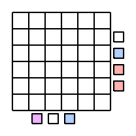
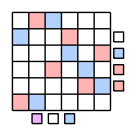

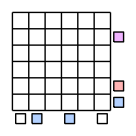
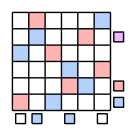

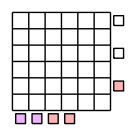
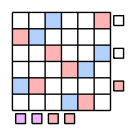

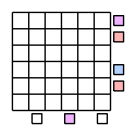
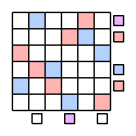

## 4x4 letters

-Graphics-  -Graphics-

-Graphics-  -Graphics-

-Graphics-  -Graphics-

«85 more identical outputs»

## 5x5 letters w/o 0

-Graphics-  -Graphics-

-Graphics-  -Graphics-

-Graphics-  -Graphics-

«5 more identical outputs»

## 5x5 letters with 0

-Graphics-  -Graphics-

-Graphics-  -Graphics-

-Graphics-  -Graphics-

«1 more identical outputs»

## 6x6 letters